# NG^23 T_06. Метод опорных векторов: ядра и штрафы

Ковалевская Варвара
14-мар-2023

## 1. Оптимизация вычисления ядра

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Train = Import["NG23T06Problem.xlsx",{"Sheets","Ковалевская Варвара"}]]
```

{4759,3}

```mathematica
Map[Dimensions,{X=Rationalize@Train[[2;;1000, ;; 2]], Y=Rationalize@Train[[2;;1000,3]]}]
lenX=Length@X
```

{{999,2},{999}}

999

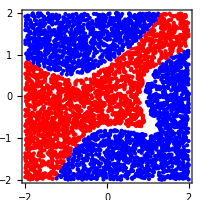

```mathematica
Graphics[{PointSize@Small,{#3/.{-1.->Blue,1.->Red},Point@{#1,#2}}&@@@Rest@Train},ImageSize->200,Frame->True,AspectRatio->Automatic]
```

```mathematica
Ker1=(#1.#2+1)^4&
Ker2= Compile[{{x1,_Real,1},{x2,_Real,1}},(x1.x2+1)^4]
Ker3= Compile[{{x1,_Real,1},{x2,_Real,1}},(x1.x2+1)^4,Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]
```

(#1.#2+1)^4&

CompiledFunction[…]

CompiledFunction[…]

```mathematica
ByteCount/@{Ker1,Ker2,Ker3}
```

{376,2240,2248}

```mathematica
res=ConstantArray[,{3,8}]
```

{{Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null}}

### Function

#### Последовательно

```mathematica
res[[1,2]]=First@Timing[Table[Y[[r]] Y[[c]] Ker1[X[[r]],X[[c]]],{r,lenX},{c,lenX}];]
```

2.67188

```mathematica
res[[1,1]]=First@Timing[Table[Yr Yc, {Yr,Y},{Yc,Y}] Table[Ker1[Xr,Xc],{Xr,X},{Xc,X}];]
```

1.60938

```mathematica
res[[1,3]]=First@Timing[Array[Y[[#1]] Y[[#2]] Ker1[X[[#1]],X[[#2]]]&, {lenX,lenX}];]
```

0.28125

```mathematica
res[[1,4]]=First@Timing[Outer[Times,Y,Y] Outer[Ker1,X,X,1];]
```

1.42188

#### Параллельно

```mathematica
res[[1,6]]=First@Timing[ParallelTable[Y[[r]] Y[[c]] Ker1[X[[r]],X[[c]]],{r,lenX},{c,lenX}];]
```

0.203125

```mathematica
res[[1,5]]=First@Timing[ParallelTable[Yr Yc, {Yr,Y},{Yc,Y}] ParallelTable[Ker1[Xr,Xc],{Xr,X},{Xc,X}];]
```

0.4375

```mathematica
res[[1,7]]=First@Timing[ParallelArray[Y[[#1]] Y[[#2]] Ker1[X[[#1]],X[[#2]]]&, {lenX,lenX}];]
```

0.03125

```mathematica
res[[1,8]]=First@Timing[Parallelize@Outer[Times,Y,Y] Parallelize@Outer[Ker1,X,X,1];]
```

0.609375

### Compile

#### Последовательно

```mathematica
res[[2,2]]=First@Timing[Table[Y[[r]] Y[[c]] Ker2[X[[r]],X[[c]]],{r,lenX},{c,lenX}];]
```

1.90625

```mathematica
res[[2,1]]=First@Timing[Table[Yr Yc, {Yr,Y},{Yc,Y}] Table[Ker2[Xr,Xc],{Xr,X},{Xc,X}];]
```

0.859375

```mathematica
res[[2,3]]=First@Timing[Array[Y[[#1]] Y[[#2]] Ker2[X[[#1]],X[[#2]]]&, {lenX,lenX}];]
```

0.328125

```mathematica
res[[2,4]]=First@Timing[Outer[Times,Y,Y] Outer[Ker2,X,X,1];]
```

0.6875

#### Параллельно

```mathematica
res[[2,6]]=First@Timing[ParallelTable[Y[[r]] Y[[c]] Ker2[X[[r]],X[[c]]],{r,lenX},{c,lenX}];]
```

0.234375

```mathematica
res[[2,5]]=First@Timing[ParallelTable[Yr Yc, {Yr,Y},{Yc,Y}] ParallelTable[Ker1[Xr,Xc],{Xr,X},{Xc,X}];]
```

0.484375

```mathematica
res[[2,7]]=First@Timing[ParallelArray[Y[[#1]] Y[[#2]] Ker1[X[[#1]],X[[#2]]]&, {lenX,lenX}];]
```

0.03125

```mathematica
res[[2,8]]=First@Timing[Parallelize@Outer[Times,Y,Y] Parallelize@Outer[Ker1,X,X,1];]
```

0.65625

### Compile+

#### Последовательно

```mathematica
res[[3,2]]=First@Timing[Table[Y[[r]] Y[[c]] Ker3[X[[r]],X[[c]]],{r,lenX},{c,lenX}];]
```

1.89063

```mathematica
res[[3,1]]=First@Timing[Table[Yr Yc, {Yr,Y},{Yc,Y}] Table[Ker3[Xr,Xc],{Xr,X},{Xc,X}];]
```

0.859375

```mathematica
res[[3,3]]=First@Timing[Array[Y[[#1]] Y[[#2]] Ker3[X[[#1]],X[[#2]]]&, {lenX,lenX}];]
```

0.28125

```mathematica
res[[3,4]]=First@Timing[Outer[Times,Y,Y] Outer[Ker3,X,X,1];]
```

0.734375

#### Параллельно

```mathematica
res[[3,6]]=First@Timing[ParallelTable[Y[[r]] Y[[c]] Ker3[X[[r]],X[[c]]],{r,lenX},{c,lenX}];]
```

0.1875

```mathematica
res[[3,5]]=First@Timing[ParallelTable[Yr Yc, {Yr,Y},{Yc,Y}] ParallelTable[Ker3[Xr,Xc],{Xr,X},{Xc,X}];]
```

0.484375

```mathematica
res[[3,7]]=First@Timing[ParallelArray[Y[[#1]] Y[[#2]] Ker3[X[[#1]],X[[#2]]]&, {lenX,lenX}];]
```

0.03125

```mathematica
res[[3,8]]=First@Timing[Parallelize@Outer[Times,Y,Y] Parallelize@Outer[Ker3,X,X,1];]
```

0.546875

## Таблица

```mathematica
res1=Prepend[res,{"TableEnum", "TableInd", "Array", "Outer", "TableEnum", "TableInd", "Array", "Outer"}]
```

{{TableEnum,TableInd,Array,Outer,TableEnum,TableInd,Array,Outer},{1.60938,2.67188,0.28125,1.42188,0.4375,0.203125,0.03125,0.609375},{0.859375,1.90625,0.328125,0.6875,0.484375,0.234375,0.03125,0.65625},{0.859375,1.89063,0.28125,0.734375,0.484375,0.1875,0.03125,0.546875}}

```mathematica
spis1={"Ядро","Funtion","Compile","Compile+"}
```

{Ядро,Funtion,Compile,Compile+}

```mathematica
res2=MapThread[Prepend,{res1,spis1}]
```

{{Ядро,TableEnum,TableInd,Array,Outer,TableEnum,TableInd,Array,Outer},{Funtion,1.60938,2.67188,0.28125,1.42188,0.4375,0.203125,0.03125,0.609375},{Compile,0.859375,1.90625,0.328125,0.6875,0.484375,0.234375,0.03125,0.65625},{Compile+,0.859375,1.89063,0.28125,0.734375,0.484375,0.1875,0.03125,0.546875}}

```mathematica
res3=PrependTo[res2,{"Матрица","Последовательно",SpanFromLeft,SpanFromLeft,"Параллельно",SpanFromLeft,SpanFromLeft}]
```

{{Матрица,Последовательно,,,Параллельно,,},{Ядро,TableEnum,TableInd,Array,Outer,TableEnum,TableInd,Array,Outer},{Funtion,1.60938,2.67188,0.28125,1.42188,0.4375,0.203125,0.03125,0.609375},{Compile,0.859375,1.90625,0.328125,0.6875,0.484375,0.234375,0.03125,0.65625},{Compile+,0.859375,1.89063,0.28125,0.734375,0.484375,0.1875,0.03125,0.546875}}

```mathematica
Grid[res3,Frame->All]
```

Матрица | Последовательно |  |  | Параллельно |  |  |  | 
Ядро | TableEnum | TableInd | Array | Outer | TableEnum | TableInd | Array | Outer
Funtion | 1.60938 | 2.67188 | 0.28125 | 1.42188 | 0.4375 | 0.203125 | 0.03125 | 0.609375
Compile | 0.859375 | 1.90625 | 0.328125 | 0.6875 | 0.484375 | 0.234375 | 0.03125 | 0.65625
Compile+ | 0.859375 | 1.89063 | 0.28125 | 0.734375 | 0.484375 | 0.1875 | 0.03125 | 0.546875

## 2. Радиально-базисная функция Гаусса в качестве ядра

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Train = Import["NG23T06Problem.xlsx",{"Sheets","Ковалевская Варвара"}]]
```

{4759,3}

```mathematica
Map[Dimensions,{X=Train[[2;;, ;; 2]], Y=Rationalize@Train[[2;;,3]]}]
lenX=Length@X
```

{{4758,2},{4758}}

4758

```mathematica
Fig0=Graphics[{PointSize@Small,{#3/.{-1.->Blue,1.->Red},Point@{#1,#2}}&@@@Rest@Train},ImageSize->200,Frame->True,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Length[iCold=Flatten@Position[Y,-1,1]]
Length[iWarm=Flatten@Position[Y,+1,1]]
{lenX, %%+%}
```

2719

2039

{4758,4758}

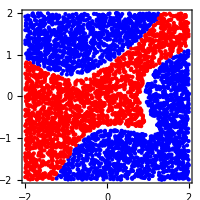

```mathematica
Fig0=Graphics[{PointSize@Small,Blue,Point@X[[iCold]],Red,Point@X[[iWarm]]},ImageSize->200,Frame->True,AspectRatio->Automatic]
```

```mathematica
σ=1;
With[{x=-0.5 σ^-2},
Ker = Compile[{{x1,_Real,1},{x2,_Real,1}},Exp[x #.#&[x1-x2]],Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]]
```

CompiledFunction[…]

```mathematica
Plot3D[Ker[{0,0},{x,y}],{x,-2,2},{y,-2,2},ColorFunction->"Rainbow",PlotRange->All]
```

-Graphics3D-

```mathematica
iS=RandomSample[Range@lenX,4]
iC={}
Length[iO=Complement[Range@lenX,iS]]
surCharge=500;
w0=.324;
Λs=RandomReal[2,4]
```

{4518,923,3121,1675}

{}

4754

{1.01209,0.713479,1.81549,0.571753}

```mathematica
ClearAll[SVM];
SVM[x_]:=Total@MapThread[#1 #2 Ker[#3,x]&,{Λs,Y[[iS]],X[[iS]]}]+surCharge Total@MapThread[#1 Ker[#3,x]&,{Y[[iC]],X[[iC]]}]-w0;
```

```mathematica
SVM@{1,-2}
```

-0.378458

```mathematica
CreatePalette@Dynamic@Show[Fig0, ContourPlot[SVM@{x,y},{x,-2.1,2.1},{y,-2.1,2.1},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Directive[Gray,Dashed],Opacity[1,Red]},ContourShading->{Opacity[0.2,Blue],None,Opacity[0.2,Red]}],
Graphics[{AbsoluteThickness@3,Green,Circle[#,Offset@3]&/@X[[iS]]}],
Graphics[{AbsoluteThickness@3,Gray,Circle[#,Offset@3]&/@X[[iC]]}],Frame->False];
```

```mathematica
Timing@Dimensions[Q=ParallelArray[Y[[#1]] Y[[#2]] Ker[X[[#1]],X[[#2]]]&,{lenX,lenX}]]
```

{1.35938,{4758,4758}}

## 3. Инициализация множества опорных точек

```mathematica
iS={sCold=RandomChoice@iCold}
```

{95}

```mathematica
sWarm = iWarm[[First@Nearest[XX[[iWarm]]->"Index",XX[[sCold]]]]]
```

128

```mathematica
4;
iS=Union@@Table[FixedPoint[(iS={sCold,sWarm=iWarm[[First@Nearest[XX[[iWarm]]->"Index",XX[[sCold]]]]]};
iS={sCold=iCold[[First@Nearest[XX[[iCold]]->"Index",XX[[sWarm]]]]],sWarm})&,
iS={sCold=RandomChoice@iCold}],
{%}]
```

{11,33,39,77,121,159}

```mathematica
ClearAll[InitSupport];
InitSupport[counter_]:=With[{sCold,sWarm},Map[Length,{iS=Union@@Table[FixedPoint[{{sCold,sWarm=iWarm[[First@Nearest[X[[iWarm]]->"Index",X[[sCold]],1]]]},
{sCold=iCold[[First@Nearest[X[[iCold]]->"Index",X[[sWarm]],1]]],sWarm}}&,
{sCold=RandomChoice@iCold}],
{Max[1,counter]}],iC={},iO=Complement[Range@lenX,iS]}]]
```

## 4. Решение задачи квадратичной оптимизации

```mathematica
Λ=Table[Subscript[λ, s],{s,iS}]
```

{λ_4518,λ_923,λ_3121,λ_1675}

```mathematica
Total[Λ.Q[[iS,iC]]]
```

0

```mathematica
iC={}
```

{}

```mathematica
{0.5 Q[[iS,iS]].Λ.Λ+
surCharge Total[Λ.Q[[iS,iC]]]-
Total@Λ//Expand,
Λ.Y[[iS]]+surCharge Total@Y[[iC]]==0,
Sequence@@Thread[-10≤Λ]}
solΛ=FindArgMin[%,Λ]
```

{-λ_923+0.5 λ_923^2-λ_1675-0.554205 λ_923 λ_1675+0.5 λ_1675^2-λ_3121+0.345885 λ_923 λ_3121-0.694567 λ_1675 λ_3121+0.5 λ_3121^2-λ_4518+0.115436 λ_923 λ_4518-0.495812 λ_1675 λ_4518+0.782538 λ_3121 λ_4518+0.5 λ_4518^2,-λ_923+λ_1675-λ_3121-λ_4518==0,-10≤λ_4518,-10≤λ_923,-10≤λ_3121,-10≤λ_1675}

{0.268528,1.92861,2.70714,4.90428}

```mathematica
w0 = 0;
w0 = Median[SVM/@X[[iS]]-Y[[iS]]]
```

0.822004

```mathematica
ClearAll[SolveQP];
SolveQP[iS_,iC_,surCharge_]:=With[{w0=0,Λ=Table[Subscript[λ, s],{s,iS}]},{FindArgMin[{0.5 Q[[iS,iS]].Λ.Λ+
surCharge Total[Λ.Q[[iS,iC]]]-
Total@Λ//Expand,
Λ.Y[[iS]]+surCharge Total@Y[[iC]]==0,
Sequence@@Thread[-10≤Λ]},Λ], Median[SVM/@X[[iS]]-Y[[iS]]]}]
```

```mathematica
SolveQP[iS,iC,surCharge]
```

{{0.268528,1.92861,2.70714,4.90428},0.}

## 5.Опорные точки и точки-нарушители

### Опорные

```mathematica
iS
solΛ
```

{4518,923,3121,1675}

{0.268528,1.92861,2.70714,4.90428}

```mathematica
Min@solΛ
If[%<0,i=Extract[iS,Position[solΛ,%,1,1]];iO=Union[iO,i];iS=Complement[iS,i],"OK"]
```

0.268528

OK

### Внутренние и точки-нарушители

```mathematica
Length[m0=SVM/@X[[iO]]]
```

4754

```mathematica
Min@m0
```

-1.70701

```mathematica
RandomChoice@Position[m0,m_/;m≤1]
List@Extract[iO,%]
iS=Union[iS,%]
iO=Complement[iO,%%];
```

{2943}

{2945}

{923,1675,2945,3121,4518,4664}